## Position from Velocity — Constant Acceleration

## Started in class, January 21, 2025 Finished version due before class, January 24, 2025

I was going to give you guys a finished notebook, and indeed I have a finished notebook that does a fancy job of what you are about to do below, but I decided that it is much better for you to produce the core code.

### The Constant Acceleration Worksheet

In the last class, we manually applied the theory to the problem with constant acceleration.

We used the midpoint approximation, we chose Δt=0.4, we chose v(t)=6·t, and we iterated from t_initial=0.0 to t_final=6.0 by applying these formulas 15 times: 

t_(i+1)=t_i+Δt

x(t_(i+1))≈x(t_i)+v(t_i+Δt/2)·Δt

The index i in our example ranged from 0 to 15 with t_0=t_initial and t_15=t_final. This gave us 15 times steps and 16 points (counting both the initial and final ones).

Here is a function and some variables that capture everything about the specific problem we are trying to solve.

```mathematica
v[t_]:=6t;
steps = 15;
tInitial=0.0;
tFinal=6.0;
deltaT=(tFinal-tInitial)/steps;
```

### An Inelegant Solution

The following works, but it is lousy programming (the kind of inelegant, inefficient programming most people do most of the time). I put it here so that you know what you are trying to get to. Don’t even bother reading this lousy code.

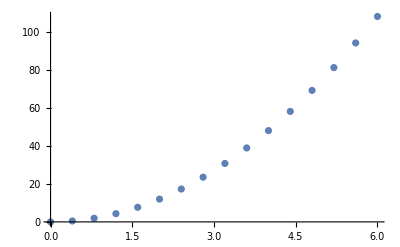

```mathematica
times = Range[tInitial,tFinal,deltaT];
midpointTimes=Drop[times,-1]+0.2; (* drop the last element which is 6.2 *)
midpointVelocities=6midpointTimes; (* our velocity function is just 6 t *)
displacements = midpointVelocities deltaT; (* the product of velocity and deltaT gives displacement *)
positions = Accumulate[displacements]; 
positions = Prepend[positions,0.0]; (* Accumulate didn't give us the initial position of 0.0, so we need to explicitly prepend it *)
orderedPairs=Transpose[{times,positions}]; (* we have a list of times and a list of positions and we need ordered pairs to feed to ListPlot *)
ListPlot[orderedPairs]
```

### The Form of an Elegant Solution

I want you to do a much more elegant solution that uses the ideas I showed you in the Heads or Tails notebook. Specifically, I want you define a function that takes the current time and the current position, and then uses the theory to compute the next time and the next position. Then I want you to use NestList to get all 15 positions. You’ll be building out something like this:

```mathematica
procedure[t_]:=t+deltaT
results=NestList[procedure,0,15];
ListPlot[results];
```

This is going to be trickier than it looks, because the function procedure that we just defined takes one argument and returns one value and that is the only kind of function that NestList can handle. How on Earth are you going to supply both t_i and x_i to procedure? How on Earth are you going to return t_(i+1) and x_(i+1) from procedure?

### Your Elegant Solution

The rain in Spain falls mainly on the plane (while you are sitting on the tarmac, waiting to fly home).